```mathematica
DSolve[√(x^2+y[x]^2)==y'[x],y[x],x]
```

DSolve[√(x^2+y[x]^2)==y'[x],y[x],x]

```mathematica
Manipulate[Plot[Evaluate[y[x] /. NDSolve[{β*Sqrt[Derivative[1][y][x]^2 + 1] == Derivative[2][y][x], y[10] == 10, y[-10] == 10}, y[x], {x, -10, 10}]], {x, -10, 10}, PlotRange -> {{-10, 10}, {0, 10}}], 
  {{β, 0.052300000000000006}, 0.01, 0.1}]
```

```mathematica
DSolve[{β √((y'[x])^2+1)==y''[x],y[0]==1,y'[0]==0},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→(1+β-Cosh[x β])/β},{y[x]→(-1+β+Cosh[x β])/β}}

```mathematica
Show[
Graphics[Line[{{10,0},{10,10}}]],
Graphics[Line[{{-10,0},{-10,10}}]],
Graphics[Point[{10,10}],PointSize[.3]],
Graphics[Point[{-10,10}],PointSize[.3]],
]
```

-Graphics-

```mathematica
Manipulate[Show[
Graphics[Line[{{10,0},{10,10}}]],
Graphics[Line[{{-10,0},{-10,10}}]],
Graphics[Point[{10,10}],PointSize[.3]],
Graphics[Point[{-10,10}],PointSize[.3]],
Plot[Evaluate[
y[x] /. NDSolve[{β/9.81 √(y'[x]^2+1) == y''[x],
 y[10] == 10, y[-10] == 10},
 y[x], {x, -10, 10}]], 
{x, -10, 10}], 
Plot[Evaluate[
y[x] /. NDSolve[{β/9.81== y''[x],
 y[10] == 10, y[-10] == 10},
 y[x], {x, -10, 10}]], 
{x, -10, 10},PlotStyle->Red],
Graphics[Text["β="<>ToString[β*1000]<>"g/m",{0,10}]]],
  {β, .1, 1.5}]
```

```mathematica
p[β_] := Plot[Evaluate[
y[x] /. NDSolve[{β √(y'[x]^2+1) == y''[x],
 y[10] == 10, y[-10] == 10},
 y[x], {x, -10, 10}]], 
{x, -10, 10}]
```

SetDelayed::write: Tag Graphics in (GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], LineBox[List[List[-9.999999591836735`, 9.999999917822041`], List[-9.993865641588808`, 9.998765337484585`], List[-9.98773169134088`, 9.997531503832692`], List[-9.975463790845026`, 9.995066138782027`], List[-9.950927989853316`, 9.99014461611831`], List[-9.901856387869898`, 9.98033839730113`], List[-9.803713183903064`, 9.960873290321025`], List[-9.607426775969392`, 9.92253207136974`], List[-9.181832858290827`, 9.842094592971122`], List[-8.784442328596958`, 9.770313568029591`], List[-8.394847023622479`, 9.703053991258715`], List[-7.972230616836778`, 9.633574606162105`], List[-7.577817598035772`, 9.571995573713235`], List[-7.150383477423544`, 9.508814190783239`], List[-6.730744581530707`, 9.450376163003448`], List[-6.339309073622564`, 9.3990694123804`], List[-5.9148524639032`, 9.346925378690315`], List[-5.518599242168532`, 9.301521042154917`], List[-5.130141245153254`, 9.260076800594817`], List[-4.708662146326754`, 9.21854123655128`], List[-4.31538643548495`, 9.183003563273079`], List[-3.8890896228319227`, 9.147988781594922`], List[-3.470588034898286`, 9.117160507305972`], List[-3.080289834949345`, 9.091574189372992`], List[-2.6569705331891815`, 9.067273856343123`], List[-2.65079684703644`, 9.066946017502794`], List[-2.6446231608836985`, 9.066618942021995`], List[-2.632275788578215`, 9.065967081119066`], List[-2.607581043967248`, 9.064672519409045`], List[-2.5581915547453145`, 9.062120035271418`], List[-2.459412576301448`, 9.057161615474737`], List[-2.261854619413714`, 9.047830903083101`], List[-2.2551649785451717`, 9.047528627867347`], List[-2.2484753376766298`, 9.04722724858809`], List[-2.235096055939546`, 9.046627177817495`], List[-2.208337492465378`, 9.045437787277887`], List[-2.1548203655170415`, 9.043102009017604`], List[-2.0477861116203693`, 9.038602454487283`], List[-2.0410964707518273`, 9.038328846641795`], List[-2.0344068298832854`, 9.038056134568034`], List[-2.0210275481462014`, 9.037513397716184`], List[-1.9942689846720332`, 9.036438673059425`], List[-1.9407518577236968`, 9.034332218861378`], List[-1.8337176038270244`, 9.030291282564832`], List[-1.827149763344723`, 9.030050788866454`], List[-1.8205819228624214`, 9.029811158474693`], List[-1.8074462418978183`, 9.029334487594504`], List[-1.781174879968612`, 9.028391505332607`], List[-1.7286321561101996`, 9.026546977896523`], List[-1.6235467083933746`, 9.02302366432613`], Skeleton[224]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 9.`]], Rule[Method, List[]], Rule[PlotRange, List[List[-10, 10], List[8.996662318299734`, 9.999999924014855`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]) is Protected.

$Failed

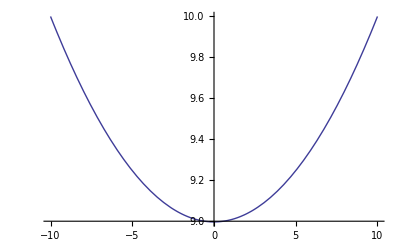
(-Graphics-)[0.1]

```mathematica
p[.1]
```

```mathematica
p[.0001]
```

(-Graphics-)[0.0001]

```mathematica
Solve[β 10^2+a 10 + b == 10&&β 10^2-a 10 + b == 10,{a,b}]
```

{{a→0,b→10-100 β}}